Zadatak 1. Napisati program koji za dati skup čvorova nalazi nalazi polinom n - tog stepena koji ih najbolje aproksimira, u smislu najmanjih kvadrata.

```mathematica
mnk[cv_, {t,st_}]:= Module[{m,a,b,koef,pol},
m=Length[cv];
a=Table[1,{i,1,m},{j,1,st+1}];
Do[
a⟦i,j⟧=cv⟦i,1⟧^(j-1),
{i,1,m},{j,2,st+1}
];
b=Table[{cv⟦i,2⟧},{i,1,m}];
koef=LinearSolve[Transpose[a].a,Transpose[a].b];
pol=0;
Do[
pol=pol+koef⟦i,1⟧*t^(i-1),
{i,1,st+1}
];
pol
]
```

```mathematica
cv={{1,1},{2,2.1},{3,3.7},{4,5},{5,6.8}}
```

{{1,1},{2,2.1},{3,3.7},{4,5},{5,6.8}}

```mathematica
pol2[t_]=mnk[cv,{t,2}]
```

-0.08+0.978571 t+0.0785714 t^2

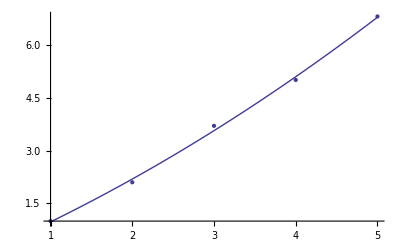

```mathematica
Show[Plot[pol2[t],{t,1,5}],ListPlot[cv],PlotRange->All]
```

```mathematica
Fit[cv,{1,t},t]
```

-0.63+1.45 t

Zadatak 2. U tabeli su data pobednička vremena ženske plivačke štafete 4 x 100m slobodnim stilom.
		OI | 1996 | 2000 | 2004 | 2012 | 2016
vreme | 3:39.29 | 3:36.61 | 3:35.94 | 3:33.15 | 3:30.65
a) Naći linearnu funkciju, koja najbolje aproksimira ove podatke (u smislu najmanjih kvadrata) i na jednom grafiku nacrtati date podatke i dobijenu funkciju.
b) Pomoću dobijenog polinoma proceniti pobedničko vreme na OI 2008. Ako je poznato da je na tim OI pobedničko vreme bilo 3:33.76, naći apsolutnu i relativnu grešku ove aproksimacije.

```mathematica
cv={{1996,3*60+39.29},{2000,3*60+36.61},{2004,3*60+35.94},{2012,3*60+33.15},{2016,3*60+30.65}}
```

{{1996,219.29},{2000,216.61},{2004,215.94},{2012,213.15},{2016,210.65}}

```mathematica
pol[t_]=Fit[cv,{1,t},t]
```

1007.92-0.395291 t

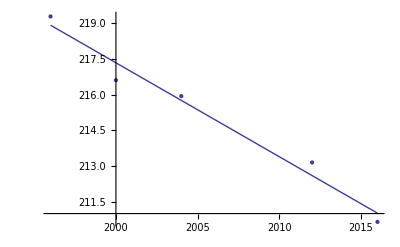

```mathematica
Show[Plot[pol[t],{t,1996,2016}],ListPlot[cv],PlotRange->All]
```

```mathematica
prib=pol[2008]
```

214.179

```mathematica
tac=3*60+33.76
```

213.76

```mathematica
ag=Abs[prib-tac]
```

0.419302

```mathematica
ag/Abs[tac]
```

0.00196156

```mathematica
cv={{5,7},{3,4},{2,2},{8,-5}}
```

{{5,7},{3,4},{2,2},{8,-5}}

```mathematica
Sort[cv]
```

{{2,2},{3,4},{5,7},{8,-5}}